```mathematica
ResourceFunction["DarkMode"][False]
```

### Constants

```mathematica
abbrev=Association[
  "Atlanta"->"ATL","Boston"->"BOS", "Brooklyn"->"BKN","Charlotte"->"CHA","Chicago"->"CHI","Cleveland"->"CLE","Dallas"->"DAL","Denver"->"DEN","Detroit"->"DET","Golden State"->"GSW","Houston"->"HOU","Indiana"->"IND","LAClippers"->"LAC","LALakers"->"LAL","Memphis"->"MEM","Miami"->"MIA","Milwaukee"->"MIL","Minnesota"->"MIN","NewOrleans"->"NOP","NewYork"->"NYK","Oklahoma City"->"OKC","Orlando"->"ORL","Philadelphia"->"PHI","Phoenix"->"PHX",
  "Portland"->"POR","Sacramento"->"SAC","SanAntonio"->"SAS","Toronto"->"TOR","Utah"->"UTA","Washington"->"WAS","GoldenState"->"GSW"
];
```

```mathematica
abbrev2=Association[
  "Atlanta Hawks"->"ATL","Boston Celtics"->"BOS", "Brooklyn Nets"->"BKN",  "Charlotte Hornets"->"CHA", "Chicago Bulls"->"CHI","Cleveland Cavaliers"->"CLE","Dallas Mavericks"->"DAL", "Denver Nuggets"->"DEN","Detroit Pistons"->"DET",  "Golden State Warriors"->"GSW",  "Houston Rockets"->"HOU",  "Indiana Pacers"->"IND","Los Angeles Clippers"->"LAC","Los Angeles Lakers"->"LAL", "Memphis Grizzlies"->"MEM",  "Miami Heat"->"MIA","Milwaukee Bucks"->"MIL", "Minnesota Timberwolves"->"MIN","New Orleans Pelicans"->"NOP","New York Knicks"->"NYK","Oklahoma City Thuner"->"OKC", "Orlando Magic"->"ORL","Philadelphia 76ers"->"PHI","Phoenix Suns"->"PHX", "Portland Trail Blazers"->"POR","Sacramento Kings"->"SAC", "San Antonio Spurs"->"SAS","Toronto Raptors"->"TOR","Utah Jazz"->"UTA",
  "Washington Wizards"->"WAS"
];
```

```mathematica
abbrevInv = Association[Reverse/@ Normal[abbrev]];
```

### Book Data

```mathematica
getReturnRate[moneyLine_]:=If[Positive[moneyLine], moneyLine/100, 100/Abs[moneyLine]]
```

```mathematica
bookData = Import["Downloads/NBABettingData - 21-22.csv", "Dataset", "HeaderLines"->1];
home = Select[bookData, #VH == "H"&];
visitors = Select[bookData, #VH == "V"&];
colNames = Normal[Keys[visitors[1, All]]];
visAway = visitors[All, AssociationThread[StringJoin["Away", #]&/@colNames, colNames]];
bookGames = Dataset[MapThread[Join[#1, #2]&, Normal/@{home, visAway}]];
```

```mathematica
filtered = Select[bookGames,getCoachWinPCT[#AwayTeam]<getCoachWinPCT[#Team]&];
```

```mathematica
Length[filtered]
```

```mathematica
revs = If[#AwayFinal> #Final, 10*getReturnRate[#AwayML], -10]&/@ filtered;
Length[revs]
N[Total[revs]]
ListLinePlot[Accumulate[Normal[revs]]]
```

```mathematica
filtered = Select[games,getCoachWinPCT[#AwayTeam]>getCoachWinPCT[#Team]&];
```

```mathematica
revs = If[#Final> #AwayFinal, 10*getReturnRate[#ML], -10]&/@ filtered;
Length[revs]
N[Total[revs]]
ListLinePlot[Accumulate[Normal[revs]]]
```

```mathematica
Histogram[Join[games[All, "ML"], games[All, "AwayML"]]]
```

### Coach Data

```mathematica
coachData = Import["Projects/Wolfram/ProbabilityResearch/CoachData21-22.csv", "Dataset"];
```

Import::nffil: File Projects/Wolfram/ProbabilityResearch/CoachData21-22.csv not found during Import.

```mathematica
teamsBook= Union[Normal[data[All, "Team"]]];
```

```mathematica
getCoachWinPCT[teamName_]:= Module[{row},
row = Normal[SelectFirst[coachData, abbrev[teamName] == #[[2]]&]];
If[!MissingQ[row], row[[16]],Missing[]]]
```

```mathematica
coachWinPCTs = DeleteMissing[getCoachWinPCT/@Keys[abbrev]];
```

### Box score data

```mathematica
dsSeason = Import["Projects/Wolfram/ProbabilityResearch/NBAResults21-22.csv", "Dataset"];
```

```mathematica
boxTeams = Union[Normal[dsSeason[[2;;]][[All, 3]]]];
```

### Match Boxscore Games to Betting Line Games

```mathematica
getGameLine[boxScore_]:=Module[{dateMonthDay, dayGames},
dateMonthDay =Interpreter["Number"][DateString[FromDateString[boxScore[[1]]], {"Month", "Day"}]];
dayGames = Select[bookGames, #Date == dateMonthDay&];
Normal[SelectFirst[dayGames, abbrev[#Team] == abbrev2[boxScore[[5]]]&& abbrev[#AwayTeam] == abbrev2[boxScore[[3]]]&]]
]
```

### Win Loss Chart

```mathematica
getWL[team_]:= Module[{ds, wlHome, wlAway, wl}, 
ds = Select[dsSeason, #[[3]] == team|| #[[5]] == team&];
Normal[If[#[[3]] == team, If[#[[4]]>#[[6]], "AW", "AL"], If[#[[6]]>#[[4]], "HW", "HL"]]&/@ ds]
]
```

```mathematica
getHomeAwayProbs[wl_]:=
{Count[wl, "HW"]/ Count[wl, "HW"|"HL"], Count[wl, "AW"]/Count[wl, "AW"|"AL"]}
```

```mathematica
getSimWL[wl_, pwh_, pwa_] :=If[StringContainsQ[#, "H"], RandomChoice[{pwh, 1-pwh}->{1, -1}],RandomChoice[{pwa, 1-pwa}->{1, -1}] ]&/@ wl
```

```mathematica
Subdivide[pMin, pMax, 5]
```

{0.57,0.597,0.624,0.651,0.678,0.705}

```mathematica
winMax = N[Minimize[{c, 
CDF[BinomialDistribution[82,0.5], c] >= 95/100 && 
0 < c<82}, c, Integers][[1]], 3]
```

48.

```mathematica
pMin = N[Minimize[{p, 
CDF[BinomialDistribution[82,p], 52] >= 10/100 && 
0 < p<1}, p, Reals][[1]], 3]
```

Minimize::fexp: Warning: Minimize used FunctionExpand to transform the problem. Since FunctionExpand transformation rules are only generically correct, the result may not be a global minimum.

0.705

```mathematica
getpRange[nWins_,ci_:95/100, nGames_:82]:=Module[{pMin, pMax},
pMin = Maximize[{p, 
CDF[BinomialDistribution[nGames,p], nWins] >= ci && 
0 < p<1}, p, Reals][[1]];
pMax = Minimize[{p, 
CDF[BinomialDistribution[82,p], 52] <= 1-ci && 
0 < p<1}, p, Reals][[1]];
N[#, 3]&/@Subdivide[pMin, pMax, 5]
]
```

```mathematica
getWinRange[nWins_,ci_:95/100, nGames_:82]:=Module[{pMin, pMax, winMin, winMax},
pMin = Maximize[{p, 
CDF[BinomialDistribution[nGames,p], nWins] >= ci && 
0 < p<1}, p, Reals][[1]];
pMax = Minimize[{p, 
CDF[BinomialDistribution[nGames,p], nWins] <= 1-ci && 
0 < p<1}, p, Reals][[1]];
winMin = Maximize[{c, 
CDF[BinomialDistribution[nGames,pMin], c] <= 1-ci && 
0 < c<82}, c, Integers][[1]];
winMax = Minimize[{c, 
CDF[BinomialDistribution[nGames,pMax], c] >= ci && 
0 < c<82}, c, Integers][[1]];
{winMin, winMax}]
```

```mathematica
getWinRange[ps[[-1]], 80/100]
```

{52.,54.,55.,57.,58.,60.}

```mathematica
wls = getWL/@boxTeams;
ps = getHomeAwayProbs/@ wls;
wls10  = Map[If[StringContainsQ[#, "W"], 1, -1]&/@ #&, wls] ;
diffsReal = Differences[Accumulate[#], 1, 5]&/@ wls10;
```

```mathematica
wlsDict = AssociationThread[boxTeams, wls10];
```

```mathematica
simWLS = MapThread[getSimWL[#1, #2[[1]], #2[[2]]]&, {wls, ps}];
diffsSim = Differences[Accumulate[#], 1, 5]&/@ simWLS;
```

```mathematica
simWLSTable = Table[MapThread[getSimWL[#1, #2[[1]], #2[[2]]]&, {wls, ps}], 20];
diffsSimTable = Map[Differences[Accumulate[#], 1, 5]&/@ #&, simWLSTable];
```

```mathematica
ListLinePlot[Flatten[diffsReal]]
```

```mathematica
ListLinePlot[Flatten[diffsSim]]
```

```mathematica
getLinePlot[diffs_, color_:Blue]:=Module[{hist, bincentersandheights},
hist = Histogram[Flatten[diffs]];
bincentersandheights=Cases[hist,Rectangle[{xmin_,ymin_},{xmax_,ymax_},___]:>{Mean[{xmin,xmax}],ymax},All];
ListPlot[bincentersandheights, PlotStyle->color, PlotHighlighting->None]
]
```

```mathematica
simPlots = getLinePlot/@ diffsSimTable;
```

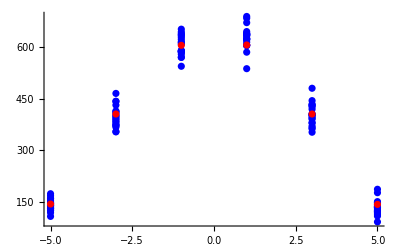

```mathematica
Show[Join[simPlots, {getLinePlot[diffsReal, Red]}], PlotRange->All]
```

```mathematica
walks = Accumulate/@wls10;
```

```mathematica
Count[#, 1]&/@ wls10
```

{43,51,45,43,46,44,52,48,23,53,20,25,42,33,56,53,51,46,36,37,24,22,51,64,27,30,34,48,49,35}

```mathematica
phx = [wlsDict["Phoenix Suns"]]
```

{-1,0,-1,-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,15,16,17,16,17,18,19,20,21,20,19,20,19,20,21,22,21,22,23,24,25,26,27,28,29,30,31,32,31,32,33,34,35,36,37,38,39,38,37,38,39,38,39,40,39,40,41,42,43,44,45,46,47,48,47,46,47,46,47,46}

```mathematica
winRangeTable = getWinRange[#, 70/100]&/@ Range[82]
```

```mathematica
sunsWinRanges = getWinRange[Count[wlsDict["Phoenix Suns"][[;;#]], 1], 70/100]&/@ Range[30,35]
```

Maximize::fexp: Warning: Maximize used FunctionExpand to transform the problem. Since FunctionExpand transformation rules are only generically correct, the result may not be a global maximum.

Minimize::fexp: Warning: Minimize used FunctionExpand to transform the problem. Since FunctionExpand transformation rules are only generically correct, the result may not be a global minimum.

Maximize::fexp: Warning: Maximize used FunctionExpand to transform the problem. Since FunctionExpand transformation rules are only generically correct, the result may not be a global maximum.

Minimize::fexp: Warning: Minimize used FunctionExpand to transform the problem. Since FunctionExpand transformation rules are only generically correct, the result may not be a global minimum.

Maximize::fexp: Warning: Maximize used FunctionExpand to transform the problem. Since FunctionExpand transformation rules are only generically correct, the result may not be a global maximum.

General::stop: Further output of Maximize::fexp will be suppressed during this calculation.

Minimize::fexp: Warning: Minimize used FunctionExpand to transform the problem. Since FunctionExpand transformation rules are only generically correct, the result may not be a global minimum.

General::stop: Further output of Minimize::fexp will be suppressed during this calculation.

{{20,30},{21,31},{21,31},{21,31},{22,32},{22,32}}

```mathematica
wlsDict["Phoenix Suns"]
```

{-1,1,-1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,1,1,-1,1,1,1,1,1,-1,-1,1,-1,1,1,1,-1,1,1,1,1,1,1,1,1,1,1,1,-1,1,1,1,1,1,1,1,1,-1,-1,1,1,-1,1,1,-1,1,1,1,1,1,1,1,1,1,-1,-1,1,-1,1,-1}

```mathematica
Quiet[getWinRange[Count[#, 1], 70/100]&/@ wls10[[;;5]]]
```

{{38,48},{46,56},{40,50},{38,48},{41,51}}

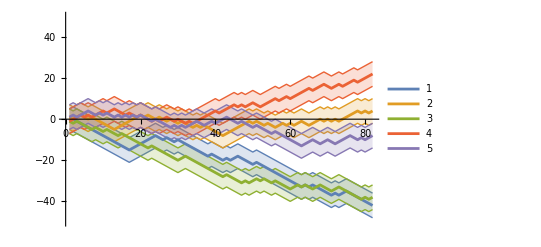

```mathematica
ListLinePlot[RandomSample[MapThread[Tooltip[Interval[#+ {6, -6}]&/@#1, #2]&, {walks, boxTeams}], 5], PlotRange->{-50, 50},PlotHighlighting->None, IntervalMarkers->"Bands", PlotLegends->Automatic]
```

```mathematica
getStandings[]
```

{Phoenix Suns,Memphis Grizzlies,Miami Heat,Golden State Warriors,Dallas Mavericks,Philadelphia 76ers,Milwaukee Bucks,Boston Celtics,Utah Jazz,Toronto Raptors,Denver Nuggets,Minnesota Timberwolves,Chicago Bulls,Cleveland Cavaliers,Brooklyn Nets,Charlotte Hornets,Atlanta Hawks,Los Angeles Clippers,New York Knicks,New Orleans Pelicans,Washington Wizards,San Antonio Spurs,Los Angeles Lakers,Sacramento Kings,Portland Trail Blazers,Indiana Pacers,Oklahoma City Thunder,Detroit Pistons,Orlando Magic,Houston Rockets}

```mathematica
getWinPCT[boxTeam_, game_:82]:= 
Count[wlsDict[boxTeam][[;;game]], 1] / game
```

```mathematica
getNWins[boxTeam_, game_:82]:=
Count[wlsDict[boxTeam][[;;game]], 1]
```

```mathematica
getStandings[game_:82]:=Module[{teams, nWins},
teams = ReverseSortBy[boxTeams, getWinPCT[#, game]&];
nWins = getNWins[#, game]&/@teams;
Transpose[{teams, nWins}]
]
```

```mathematica
getWinRange[30, 60/100, 60]
```

Maximize::fexp: Warning: Maximize used FunctionExpand to transform the problem. Since FunctionExpand transformation rules are only generically correct, the result may not be a global maximum.

Minimize::fexp: Warning: Minimize used FunctionExpand to transform the problem. Since FunctionExpand transformation rules are only generically correct, the result may not be a global minimum.

{28,32}

```mathematica
getWinRange[25, 55/100, 60]
```

Maximize::fexp: Warning: Maximize used FunctionExpand to transform the problem. Since FunctionExpand transformation rules are only generically correct, the result may not be a global maximum.

Minimize::fexp: Warning: Minimize used FunctionExpand to transform the problem. Since FunctionExpand transformation rules are only generically correct, the result may not be a global minimum.

{24,26}

```mathematica
Column[getStandings[]]
```

{Phoenix Suns,64}
{Memphis Grizzlies,56}
{Miami Heat,53}
{Golden State Warriors,53}
{Dallas Mavericks,52}
{Philadelphia 76ers,51}
{Milwaukee Bucks,51}
{Boston Celtics,51}
{Utah Jazz,49}
{Toronto Raptors,48}
{Denver Nuggets,48}
{Minnesota Timberwolves,46}
{Chicago Bulls,46}
{Cleveland Cavaliers,44}
{Brooklyn Nets,44}
{Charlotte Hornets,43}
{Atlanta Hawks,43}
{Los Angeles Clippers,42}
{New York Knicks,37}
{New Orleans Pelicans,36}
{Washington Wizards,35}
{San Antonio Spurs,34}
{Los Angeles Lakers,33}
{Sacramento Kings,30}
{Portland Trail Blazers,27}
{Indiana Pacers,25}
{Oklahoma City Thunder,24}
{Detroit Pistons,23}
{Orlando Magic,22}
{Houston Rockets,20}

```mathematica
SortBy[teams, Position[#]]
```

```mathematica
simWLSRand = Table[RandomFunction[RandomWalkProcess[.5],{0,80}], 30];
```

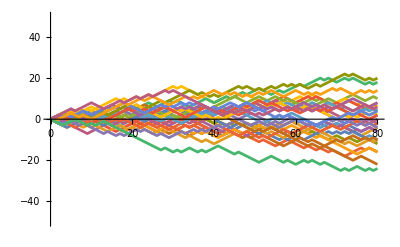

```mathematica
ListLinePlot[simWLSRand, PlotRange->{-50, 50}]
```

```mathematica
simWalks = Accumulate/@ simWLS;
```

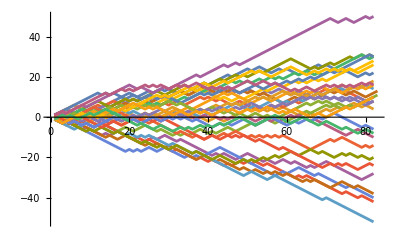

```mathematica
ListLinePlot[simWalks, PlotHighlighting->None]
```

### Bet on lines after specified streak of games

```mathematica
getTeamGames[team_]:=Select[dsSeason, #[[3]] == team|| #[[5]] == team&]
```

```mathematica
getGamesAfterSequence[seq_]:= Module[{streakPos, teamGames, sps, spsValid}, 
streakPos = SequencePosition[#, seq]& /@ wls10;
teamGames = getTeamGames/@ boxTeams;
sps = #[[All, -1]] + 1 & /@ streakPos;
spsValid = Select[#, #<=80&]&/@ sps;
DeleteMissing[MapThread[Normal[#1[[#2]]]&, {teamGames, spsValid}], 2]
]
```

```mathematica
gamesAfterSequence = getGamesAfterSequence[{-1, -1, -1}];
```

```mathematica
gameLines = DeleteMissing[Map[getGameLine, #]]& /@ gamesAfterSequence;
```

```mathematica
bet[game_, team_, amount_]:= 
If[abbrevInv[team] == game[["Team"]], 
	If[game[["Final"]] > game[["AwayFinal"]], amount*getReturnRate[game[["ML"]]], -amount], 
	If[abbrevInv[team] == game[["AwayTeam"]], 
		If[game[["Final"]] < game[["AwayFinal"]], amount*getReturnRate[game[["AwayML"]]], -amount],
		"Team is not in that game"]]
```

```mathematica
betAgainst[game_, team_, amount_]:=
If[abbrevInv[team] == game[["Team"]], 
	If[game[["Final"]] < game[["AwayFinal"]], amount*getReturnRate[game[["AwayML"]]], -amount], 
	If[abbrevInv[team] == game[["AwayTeam"]], 
		If[game[["Final"]] > game[["AwayFinal"]], amount*getReturnRate[game[["ML"]]], -amount],
		"Team is not in that game"]]
```

```mathematica
betAll[games_, team_, amount_]:=bet[#, team, amount]&/@ games
```

```mathematica
betAgainstAll[games_, team_, amount_]:= betAgainst[#, team, amount]&/@ games
```

```mathematica
revenues = MapThread[betAll[#1,#2,10]&, {gameLines, Keys[abbrevInv]}];
```

```mathematica
Length[Flatten[revenues]]
```

315

```mathematica
N[Total[Flatten[revenues]]]
```

-82.8756

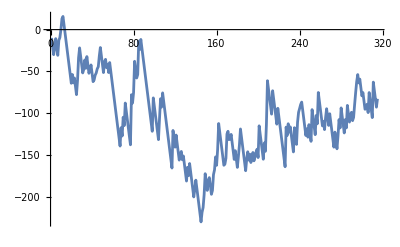

```mathematica
ListLinePlot[Accumulate[Flatten[revenues]]]
```